```mathematica
Quit[];
```

```mathematica
ClearAll["Global`*"];
```

## Obtaining the coefficients from BH Perturbation Toolkit

Not necessary for the Log Project

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<ReggeWheeler`
```

A list of ω>0 for evaluation

```mathematica
omegatabp=Join[10^Range[-4,-0.698,0.002],10^Range[-0.6999,0.017,0.001],10^Range[0.018,0.6,0.02]];
```

```mathematica
omegatabpT=Join[10^Range[-4,-0.698,0.02],10^Range[-0.6999,0.017,0.01],10^Range[0.018,0.6,0.02]];
```

```mathematica
incp=Table[ReggeWheelerRadial[-2,2,omegatabp[[i]]]["Up"]["Amplitudes"]["Incidence"],{i,1,Length[omegatabp],1}];
```

RenormalizedAngularMomentum::precision: Method "Monodromy" currently only works reliably with arbitrary precision input parameters.

General::stop: Further output of RenormalizedAngularMomentum::precision will be suppressed during this calculation.

$Aborted

```mathematica
refp=Table[ReggeWheelerRadial[-2,2,omegatabp[[i]]]["Up"]["Amplitudes"]["Reflection"],{i,1,Length[omegatabp],1}];
```

ReggeWheeler`MST`RenormalizedAngularMomentum`RenormalizedAngularMomentum::precision: Method "Monodromy" currently only works reliably with arbitrary precision input parameters.

General::stop: Further output of ReggeWheeler`MST`RenormalizedAngularMomentum`RenormalizedAngularMomentum::precision will be suppressed during this calculation.

A list of ω<0 for evaluation

```mathematica
omegatabm=Reverse[-omegatabp];
incm=Reverse[Conjugate[incp]];
refm=Reverse[Conjugate[refp]];
```

Join the two lists

```mathematica
omegataball=Join[omegatabm,omegatabp];
inc=Join[incm,incp];
ref=Join[refm,refp];
```

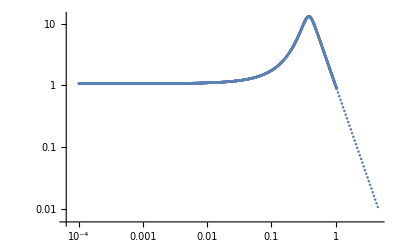

```mathematica
ListLogLogPlot[Transpose[{omegatabp,1/Abs[incp*omegatabp^3]}]]
```

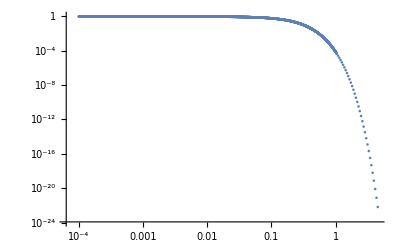

```mathematica
ListLogLogPlot[Transpose[{omegatabp,Abs[refp*omegatabp^3]}]]
```

```mathematica
Export["Coeff.h5",{"Datasets"->{"frequency"->omegataball,"inc"->inc,"ref"->ref},"DataFormat"->{Automatic,Automatic,Automatic}},"Rules"];
```

## Same Coefficients for the Teukolsky Equaiton

```mathematica
<<Teukolsky`
```

RenormalizedAngularMomentum::shdw: Symbol RenormalizedAngularMomentum appears in multiple contexts {Teukolsky`MST`RenormalizedAngularMomentum`,ReggeWheeler`MST`RenormalizedAngularMomentum`}; definitions in context Teukolsky`MST`RenormalizedAngularMomentum` may shadow or be shadowed by other definitions.

Legend: TeukolskyRadial[spin-weight, l, m, χ, ω], DCoeff.h5 are for spin-weight -2, CCoeff.h5 for +2.

```mathematica
incpT=Table[TeukolskyRadial[-2,2,2,0,omegatabp[[i]]]["Up"]["Amplitudes"]["Incidence"],{i,1,Length[omegatabp],1}];
```

```mathematica
refpT= Table[TeukolskyRadial[-2,2,2,0,omegatabp[[i]]]["Up"]["Amplitudes"]["Reflection"],{i,1,Length[omegatabp],1}];
```

```mathematica
incpT1155=Table[TeukolskyRadial[-2,2,2,0.7,omegatabp[[i]]]["Up"]["Amplitudes"]["Incidence"],{i,1,Length[omegatabp],1}];
```

```mathematica
refpT1155= Table[TeukolskyRadial[-2,2,2,0.7,omegatabp[[i]]]["Up"]["Amplitudes"]["Reflection"],{i,1,Length[omegatabp],1}];
```

```mathematica
incmT=Reverse[Conjugate[incpT]];
refmT=Reverse[Conjugate[refpT]];
```

```mathematica
incT=Join[incmT,incpT];
refT=Join[refmT,refpT];
```

Some comparison plot with Ma22

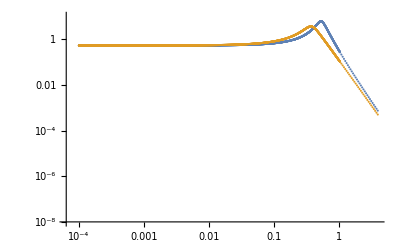

```mathematica
ListLogLogPlot[{Transpose[{omegatabp,1/Abs[incpT1155*omegatabp^4]}],Transpose[{omegatabp,1/Abs[incpT*omegatabp^4]}]}, PlotRange->{{10^-4,10^0}{10^-4,10^1}}]
```

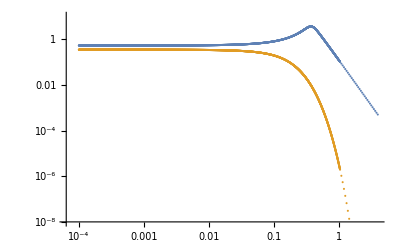

```mathematica
ListLogLogPlot[{Transpose[{omegatabp,1/Abs[incpT*omegatabp^4]}],Transpose[{omegatabp,Abs[omegatabp^5 * refpT]}]}, PlotRange->{{10^-4,10^0}{10^-4,10^1}}]
```

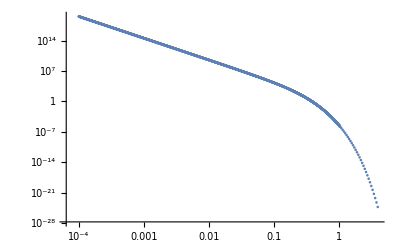

```mathematica
ListLogLogPlot[Transpose[{omegatabp,Abs[ refpT]}]]
```

```mathematica
Export["DCoeff.h5",{"Datasets"->{"frequency"->omegataball,"inc"->incT,"ref"->refT},"DataFormat"->{Automatic,Automatic,Automatic}},"Rules"];
```